CHAPTER ChapterLabel

Science and Engineering

Mmm—but it’s poetry in motion
And when she turned her eyes to me
As deep as any ocean
As sweet as any harmony
Mmm—but she blinded me with science
And failed me in geometry

When she’s dancing next to me
“Blinding me with science—science!”
“Science!”
I can hear machinery
“Blinding me with science—science!”
“Science!”

Thomas Dolby, “She Blinded Me With Science”

ChapterLabel.Heading1  Introduction

Scientists and engineers make up a large part of the Mathematica user base, and it is hard to think of any scientific or engineering practitioner, no matter how specialized, who could not benefit from Mathematica. I am neither a scientist nor an engineer by profession, but just fiddling around with Mathematica has given me insights into scientific and engineering ideas that otherwise would have taken many years of study.

The goals of this chapter are threefold. First, I want to illustrate techniques for organizing solutions to problems. Many science and engineering problems require numerous variables, and organization becomes paramount. There is not one correct way to organize complex solutions, but I provide two different approaches in Recipes 13.6 and 13.11. The second goal is to take some of the theoretical recipes covered in earlier chapters and apply them to real-world problems. I often see posts on Mathematica’s primary mailing list questioning the usefulness of function or pattern-based programming on real-world problems. Other posters express a wish to use these techniques but can’t get themselves on the right track. This chapter contains recipes to which most scientists and engineers can relate, and all use a mixture of functional and pattern-based ideas. An auxiliary goal is to take some of the functions introduced in Chapter 11 and make each the focus of a recipe. The third goal of the chapter is to introduce some special features of Mathematica that we did not have occasion to discuss in earlier recipes.

One important feature introduced in Mathematica 6 that gained momentum in version 7 is curated data sources. These high-quality data sources alone are worth the cost of admission to Mathematica’s user base. Recipes 13.1 through 13.4 discuss some sources pertinent to the sciences. Chapter 14 includes recipes related to financial data sources. All these sources have a uniform, self-describing structure. You can query any data source for the kinds of data it provides using syntax DataSource ["Properties"]. This will give you a list of properties. Each property describes an important subset of the data held by the source. You use the properties along with keys to retrieve particular values. For example, ElementData[1, "AtomicWeight"] gives 1.00794, the atomic weight of hydrogen. Once you master the data source concept, you will quickly be able to leverage new data sources as they become available.

Recipe 13.5 applies the discrete calculus function RSolve from Recipe 11.10 to solve a standard predator-prey problem. Here I also demonstrate how Mathematica’s interactive features can be used to explore the solution space and gain insight into the dynamics of the problem.

In Recipe 13.6, I solve a relatively straightforward problem in rigid body dynamics. The primary purpose of this recipe is to illustrate one way you might organize a problem with many objects and many parameters per object. This recipe highlights Mathematica’s flexible ways of creating names of things, an ability you should exploit when modeling complex problems. Recipe 13.11 uses the topic of finite element method (FEM) to illustrate an alternate way to organize a problem that uses a lot of data and a variety of related functions. The interface developed here follows a trend that is becoming more popular in new Mathematica features (e.g., LinearModelFit).

Recipes 13.7 through 13.10 focus on applied differential equations. Here I solve some problems symbolically using DSolve and some problems numerically using NDSolve. These recipes show how to set up initial and boundary conditions, how to leverage Fourier series in obtaining solutions, and how to visualize solutions.

ChapterLabel.Heading1  Working with Element Data

Problem

You want to perform computations that take as input information about the chemical elements. You may also want to create visual displays of this information for reference or classroom use.

Solution

You can list the names of all the elements using ElementData[] or the name of the nth element using ElementData[n].

```mathematica
ElementData[]
```

{Hydrogen,Helium,Lithium,Beryllium,Boron,Carbon,Nitrogen,Oxygen,Fluorine,Neon,Sodium,Magnesium,Aluminum,Silicon,Phosphorus,Sulfur,Chlorine,Argon,Potassium,Calcium,Scandium,Titanium,Vanadium,Chromium,Manganese,Iron,Cobalt,Nickel,Copper,Zinc,Gallium,Germanium,Arsenic,Selenium,Bromine,Krypton,Rubidium,Strontium,Yttrium,Zirconium,Niobium,Molybdenum,Technetium,Ruthenium,Rhodium,Palladium,Silver,Cadmium,Indium,Tin,Antimony,Tellurium,Iodine,Xenon,Cesium,Barium,Lanthanum,Cerium,Praseodymium,Neodymium,Promethium,Samarium,Europium,Gadolinium,Terbium,Dysprosium,Holmium,Erbium,Thulium,Ytterbium,Lutetium,Hafnium,Tantalum,Tungsten,Rhenium,Osmium,Iridium,Platinum,Gold,Mercury,Thallium,Lead,Bismuth,Polonium,Astatine,Radon,Francium,Radium,Actinium,Thorium,Protactinium,Uranium,Neptunium,Plutonium,Americium,Curium,Berkelium,Californium,Einsteinium,Fermium,Mendelevium,Nobelium,Lawrencium,Rutherfordium,Dubnium,Seaborgium,Bohrium,Hassium,Meitnerium,Darmstadtium,Roentgenium,Ununbium,Ununtrium,Ununquadium,Ununpentium,Ununhexium,Ununseptium,Ununoctium}

```mathematica
ElementData[1]
```

Hydrogen

Mathematica will return properties of an element if given its number and the name of the property.

```mathematica
Row[{ElementData[1],ElementData[1,"AtomicNumber"],ElementData[1,"AtomicWeight"],ElementData[1,"Phase"]},"\t"]
```

Hydrogen11.00794Gas

Discussion

You can see from the list of all properties that Mathematica has a comprehensive database of elemental data. Be aware that CommonCompoundNames will pull in a lot of data if you use it with a common element like hydrogen.

```mathematica
Partition[ElementData["Properties"],3,3,1,""]//TableForm
```

Abbreviation | AbsoluteBoilingPoint | AbsoluteMeltingPoint
AdiabaticIndex | AllotropeNames | AllotropicMultiplicities
AlternateNames | AlternateStandardNames | AtomicNumber
AtomicRadius | AtomicWeight | Block
BoilingPoint | BrinellHardness | BulkModulus
CASNumber | Color | CommonCompoundNames
CovalentRadius | CriticalPressure | CriticalTemperature
CrustAbundance | CrystalStructure | CuriePoint
DecayMode | Density | DiscoveryCountries
DiscoveryYear | ElectricalConductivity | ElectricalType
ElectronAffinity | ElectronConfiguration | ElectronConfigurationString
Electronegativity | ElectronShellConfiguration | FusionHeat
GasAtomicMultiplicities | Group | HalfLife
HumanAbundance | IconColor | IonizationEnergies
IsotopeAbundances | KnownIsotopes | LatticeAngles
LatticeConstants | Lifetime | LiquidDensity
MagneticType | MassMagneticSusceptibility | MeltingPoint
Memberships | MeteoriteAbundance | MohsHardness
MolarMagneticSusceptibility | MolarVolume | Name
NeelPoint | NeutronCrossSection | NeutronMassAbsorption
OceanAbundance | Period | Phase
PoissonRatio | QuantumNumbers | Radioactive
RefractiveIndex | Resistivity | ShearModulus
SolarAbundance | SoundSpeed | SpaceGroupName
SpaceGroupNumber | SpecificHeat | StableIsotopes
StandardName | SuperconductingPoint | ThermalConductivity
ThermalExpansion | UniverseAbundance | Valence
VanDerWaalsRadius | VaporizationHeat | VickersHardness
VolumeMagneticSusceptibility | YoungModulus |

The most obvious application of ElementData is to create a periodic table. The ElementData documentation shows code for a simple table. Here I show a more ambitious one, complete with Tooltip.

```mathematica
makeElemDetail[a_] := Module[{abr,name,atomicWeight,density,melting,boiling,color,phase}, 
{abr,name,atomicWeight,density,melting,boiling,color, phase}=Table[ElementData[a,p],{p,{"Abbreviation","StandardName","AtomicWeight","Density","MeltingPoint","BoilingPoint","Color","Phase"}}];
Grid[{{name,SpanFromLeft,a},{abr,atomicWeight,"amu"},{"Density",density,"Kg/m^3"},{"Melting Pt",melting,"C"},{"Boiling Pt.",boiling,"C"},{"Phase",color,phase}},Frame->All,Alignment->{{Left,Right,Right},{Center,Center,Center}}]
]

makeElem[a_,size_] := Module[{abr,name,atomicWeight},abr =ElementData[a,"Abbreviation"]; 
atomicWeight=ElementData[a,"AtomicWeight"];
Graphics[{Text[Style[ToString[a],9,Bold,FontFamily->"Helvetica",TextAlignment->Center],{0,20}],Text[Style[abr,20,FontWeight->"Bold",FontFamily->"Helvetica"],{0,0}],Text[Style[ToString[atomicWeight],8,FontFamily->"Helvetica",TextAlignment->Center],{0,-20}]},
ImageSize->{size,size}]]

makePeriodicTable[w_,h_] :=Module[{elemData,frame,background,re1=57,re2=71,re3=89,re4=103,gsz=42}, elemData =Table[ElementData[e,p],{e,1,118},{p,{"AtomicNumber","Period","Group"}}];
frame ={None,None,Cases[elemData,{a_Integer,p_,g_Integer} :> ({p,g} -> True)]};
background = {None,None,Cases[elemData,{a_Integer,p_,g_Integer} :> ({p,g} -> ElementData[a,"IconColor"])]};
Column[{
GraphicsGrid[Normal[SparseArray[Cases[elemData,{a_Integer,p_,g_Integer} :> ({p,g} -> a)]]] /. {a_Integer/;a>0 :>  Tooltip[makeElem[a,gsz],makeElemDetail[a]],
0-> Graphics[{}]},Frame->frame,Background->background,ImageSize->{w,h}],
GraphicsGrid[{Table[Tooltip[makeElem[a,gsz],makeElemDetail[a]],{a,re1,re2}],Table[makeElem[a,gsz],{a,re3,re4}]},ImageSize->{w-100,100},Background->{None,None,Flatten[Table[{{1,a-re1+1}->ElementData[a, "IconColor"], {2,a-re1+1}->ElementData[a + re3-re1, "IconColor"]}, {a, re1, re2}]]}]},Alignment->{Center,Automatic}]]
```

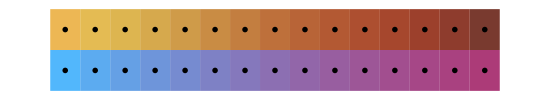
-Graphics-
-Graphics-

```mathematica
makePeriodicTable[650, 300]
```

ChapterLabel.Heading1  Working with Chemical Data

Problem

You want to perform computations that take as input information about the chemical compounds. You may also want to create visual displays of this information for reference or classroom use.

Solution

ChemicalData is a curated data source. You can request chemical information by common names, registry numbers, IUPAC-like names, or structure strings.

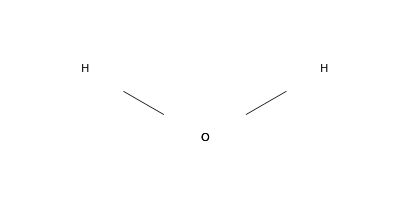

```mathematica
ChemicalData["Water"]
```

```mathematica
ChemicalData["CO2","IUPACName"]
```

carbon dioxide

```mathematica
ChemicalData["CID5234","Name"]
```

{sodium chloride,sodium chloride-35 Cl}

```mathematica
ChemicalData["Glucose","CompoundFormulaDisplay"]
```

{C_6H_12O_6,C_6H_12O_6,C_6H_12O_6,C_6H_12O_6}

```mathematica
GraphicsRow[ChemicalData["Glucose","MoleculePlot"],ImageSize->Large]
```

-Graphics-

Discussion

The list of properties of chemical compounds is quite impressive. The table below lists a random subset of the full list of 101 properties.

```mathematica
Partition[Sort[RandomSample[ChemicalData["Properties"],30]],3]//TableForm
```

AcidityConstant | BoilingPoint | CHStructureDiagram
CIDNumber | CompoundFormulaDisplay | CriticalPressure
CriticalTemperature | FlashPointFahrenheit | FormattedName
HildebrandSolubility | IUPACName | MDLNumber
MeltingPoint | NFPAHazards | NFPAHealthRating
NFPALabel | NonStandardIsotopeCount | NonStandardIsotopeNumbers
PartitionCoefficient | Phase | Resistivity
RotatableBondCount | SideChainAcidityConstant | SpaceFillingMoleculePlot
StructureDiagram | TautomerCount | TopologicalPolarSurfaceArea
VaporPressureTorr | VertexTypes | Viscosity

At the time of this writing, Mathematica has curated data on over 34,300 compounds, subdivided into 67 classes.

```mathematica
Length[ChemicalData[]]
```

34336

```mathematica
ChemicalData["Classes"]
```

{AcidAnhydrides,AcidHalides,Acids,Alcohols,Aldehydes,Alkanes,Alkenes,Alkynes,Alloys,Amides,Amines,AminoAcidDerivatives,AminoAcids,Arenes,Aromatic,Bases,Brominated,Carbohydrates,CarboxylicAcids,Catalysts,Cations,Ceramics,Chiral,Chlorinated,Dendrimers,Esters,Ethers,Fluorinated,Furans,Gases,Halogenated,HeavyMolecules,Heterocyclic,Hydrides,Hydrocarbons,Imidazoles,Indoles,Inorganic,Iodinated,IonicLiquids,Ketones,Ligands,Lipids,Liquids,MetalCarbonyls,Monomers,Nanomaterials,Nitriles,Organic,Organometallic,Oxides,Phenols,Piperazines,Piperidines,Polymers,Pyrazoles,Pyridines,Pyrimidines,Quinolines,Salts,Solids,Solvents,Sulfides,SyntheticElements,Thiazoles,Thiols,Thiophenes}

There are six kinds of structural diagrams that can be used to visualize these compounds. Here, for example, are representations for what may be one of your favorites, for better or worse—caffeine.

```mathematica
GraphicsGrid[Partition[Table[ChemicalData["Caffeine",p],{p,{"CHColorStructureDiagram",
"CHStructureDiagram","ColorStructureDiagram","StructureDiagram","MoleculePlot","SpaceFillingMoleculePlot"}}],3],ImageSize->Large]
```

-Graphics-

You can use the data to analyze relationships between properties. Here I show a plot of inverse vapor pressure to boiling point for all liquids with a Tooltip around each point so outliers are easy to identify. Cases is used to filter out any MissingData entries.

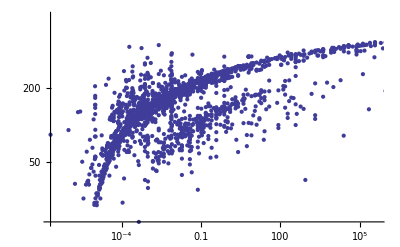

```mathematica
ListLogLogPlot[Cases[Table[{ChemicalData[c,"VaporPressure"],ChemicalData[c,"BoilingPoint"],c},{c,ChemicalData["Liquids"]}],{vp_Real,bp_Real,c_String}:> Tooltip[{1/vp,bp},c]]]
```

ChapterLabel.Heading1  Working with Particle Data

Problem

You want to perform computations that take as input information about the elementary particles. You may also want to create visual displays of this information for reference or classroom use.

Solution

```mathematica
ParticleData["Classes"]
```

{Baryon,BBBarMeson,Boson,BottomBaryon,BottomMeson,CCBarMeson,CharmedBaryon,CharmedMeson,Fermion,GaugeBoson,Hadron,Lepton,LongLived,Meson,Neutrino,Pentaquark,Quark,Stable,StrangeBaryon,StrangeCharmedBaryon,StrangeCharmedMeson,StrangeMeson,UnflavoredBaryon,UnflavoredMeson}

It is easy to create functions that generate tables of particle information. The function particleTable accepts a list of one or more class memberships (e.g., Baryon, LongLived, and others from ParticleData["Classes"]) and a list of properties to use as columns. The helper function particleData reformats "QuarkContent" into a more concise representation. You will often want to filter out entries that are missing since there is only partial data available for exotic particles.

```mathematica
particleData[p_,"QuarkContent"]:=Flatten[ ParticleData[p,"QuarkContent"]/. q_String :>   ParticleData[q,"Symbol"]]
particleData[p_,prop_]:= ParticleData[p,prop]
particleTable[memberships_List,properties_List] :=Module[{},
Grid[Prepend[
Table[particleData[particle,#]& /@ properties,{particle,Select[ParticleData[],(Intersection[ParticleData[#,"Memberships"],memberships] == memberships )&]}],properties]/. {Missing["Unknown"]->"?",Missing["NotAvailable"]->"N/A"},
Frame->All,
ItemStyle->{Automatic,Automatic,{{{1,1},{1,Length[properties]}}->Bold}}]
 ]
```

Create a table of long-lived baryons. A baryon is a particle made of three quarks, and long-lived refers to particles whose lifetime is greater than 10^(–20) seconds.

```mathematica
particleTable[{"Baryon","LongLived"},{"StandardName","Symbol","Mass","Charge","Lifetime","Isospin","QuarkContent"}]
```

StandardName | Symbol | Mass | Charge | Lifetime | Isospin | QuarkContent
Lambda | Λ | 1115.683 | 0 | 2.632×10^-10 | 0 | {s,d,u}
LambdaBar | Λ̄ | 1115.683 | 0 | 2.632×10^-10 | 0 | {s̄,d̄,ū}
Neutron | n | 939.56536 | 0 | 885.6 | 1/2 | {d,d,u}
NeutronBar | n̄ | 939.56536 | 0 | 885.6 | 1/2 | {d̄,d̄,ū}
Omega | Ω | 1672.45 | -1 | 8.21×10^-11 | 0 | {s,s,s}
OmegaBar | Ω̄ | 1672.45 | 1 | 8.21×10^-11 | 0 | {s̄,s̄,s̄}
Proton | p | 938.27203 | 1 | ∞ | 1/2 | {d,u,u}
ProtonBar | p̄ | 938.27203 | -1 | ∞ | 1/2 | {d̄,ū,ū}
SigmaBarMinus | (Σ̄)^- | 1189.37 | -1 | 8.018×10^-11 | 1 | {s̄,ū,ū}
SigmaBarPlus | (Σ̄)^+ | 1197.449 | 1 | 1.48×10^-10 | 1 | {s̄,d̄,d̄}
SigmaBarZero | (Σ̄)^0 | 1192.642 | 0 | 7.4×10^-20 | 1 | {s̄,d̄,ū}
SigmaMinus | Σ^- | 1197.449 | -1 | 1.48×10^-10 | 1 | {s,d,d}
SigmaPlus | Σ^+ | 1189.37 | 1 | 8.018×10^-11 | 1 | {s,u,u}
SigmaZero | Σ^0 | 1192.642 | 0 | 7.4×10^-20 | 1 | {s,d,u}
XiBarPlus | (Ξ̄)^+ | 1321.31 | 1 | 1.64×10^-10 | 1/2 | {s̄,s̄,d̄}
XiBarZero | (Ξ̄)^0 | 1314.83 | 0 | 2.9×10^-10 | 1/2 | {s̄,s̄,ū}
XiMinus | Ξ^- | 1321.31 | -1 | 1.64×10^-10 | 1/2 | {s,s,d}
XiZero | Ξ^0 | 1314.83 | 0 | 2.9×10^-10 | 1/2 | {s,s,u}
{LambdaB,0} | Λ_b | 5624. | 0 | 1.23×10^-12 | 0 | {b,d,u}
{LambdaBBar,0} | (Λ̄)_b | 5624. | 0 | 1.23×10^-12 | 0 | {b̄,d̄,ū}
{LambdaC,1} | Λ_c | 2286.46 | 1 | 2.×10^-13 | 0 | {c,d,u}
{LambdaCBar,-1} | (Λ̄)_c | 2286.46 | -1 | 2.×10^-13 | 0 | {c̄,d̄,ū}
{OmegaC,0} | Ω_c | 2697.5 | 0 | 6.9×10^-14 | 0 | {c,s,s}
{OmegaCBar,0} | (Ω̄)_c | 2697.5 | 0 | 6.9×10^-14 | 0 | {c̄,s̄,s̄}
{XiC,0} | Ξ_c^0 | 2471. | 0 | 1.1×10^-13 | 1/2 | {c,s,d}
{XiC,1} | Ξ_c^+ | 2467.9 | 1 | 4.42×10^-13 | 1/2 | {c,s,u}
{XiCBar,-1} | (Ξ̄)_c^- | 2467.9 | -1 | 4.42×10^-13 | 1/2 | {c̄,s̄,ū}
{XiCBar,0} | (Ξ̄)_c^0 | 2471. | 0 | 1.1×10^-13 | 1/2 | {c̄,s̄,d̄}
{XiCC,1} | Ξ_cc | 3518.9 | 1 | 3.3×10^-14 | ? | {c,c,d}
{XiCCBar,-1} | (Ξ̄)_cc | 3518.9 | -1 | 3.3×10^-14 | ? | {c̄,c̄,d̄}

Discussion

The list of properties available in particle data are as follows:

```mathematica
Transpose[Partition[ParticleData["Properties"],9,9,1,""]]//TableForm
```

Antiparticle | Excitations | Isospin | PDGNumber
BaryonNumber | FullDecayModes | IsospinMultiplet | QuarkContent
Bottomness | FullSymbol | IsospinProjection | Spin
Charge | GenericFullSymbol | LeptonNumber | Strangeness
ChargeStates | GenericSymbol | Lifetime | Symbol
Charm | GFactor | Mass | Topness
CParity | GParity | MeanSquareChargeRadius | UnobservedDecayModes
DecayModes | HalfLife | Memberships | Width
DecayType | Hypercharge | Parity |

```mathematica
ParticleData["Classes"]
```

{Baryon,BBBarMeson,Boson,BottomBaryon,BottomMeson,CCBarMeson,CharmedBaryon,CharmedMeson,Fermion,GaugeBoson,Hadron,Lepton,LongLived,Meson,Neutrino,Pentaquark,Quark,Stable,StrangeBaryon,StrangeCharmedBaryon,StrangeCharmedMeson,StrangeMeson,UnflavoredBaryon,UnflavoredMeson}

A scatter plot of mass versus spin versus charge shows large voids where there are no known particles (or where the values are unknown).

```mathematica
ListPointPlot3D[Cases[Sort[{ParticleData[#,"Mass"],ParticleData[#,"Spin"],ParticleData[#,"Charge"]}&/@ParticleData["Hadron"]],{_?NumberQ,_?NumberQ,_?NumberQ}],AxesLabel->{"mass","spin","charge"}]
```

-Graphics3D-

DecayModes and FullDecayModes list the ways the particle can decay; FullDecayModes also lists those predicted by theory but not observed in detectors. The number (or interval) display with the decay mode is the branch ratio.

```mathematica
Flatten[Table[p ->#& /@ ParticleData[p,"DecayModes"],{p,{"DeltaMinus","DeltaZero","DeltaPlus","Lambda"}}],1]//TableForm
```

DeltaMinus→{{Neutron,PiMinus},1.}
DeltaZero→{{Neutron,Photon},Interval[{0.005,0.008}]}
DeltaPlus→{{Proton,Photon},Interval[{0.005,0.008}]}
Lambda→{{Proton,PiMinus},0.639}
Lambda→{{Neutron,PiZero},0.358}
Lambda→{{Neutron,Photon},0.00175}
Lambda→{{Proton,PiMinus,Photon},0.00084}
Lambda→{{Proton,Electron,ElectronNeutrinoBar},0.000832}
Lambda→{{Proton,Muon,MuonNeutrinoBar},0.000157}

ChapterLabel.Heading1  Working with Genetic Data and 
Protein Data

Problem

You want to use Mathematica’s pattern matching and computational capabilities to develop bioinformatics applications. GenomeData and ProteinData provide the raw materials for this application.

Solution

Get the first 100 nucleobases (or, simply, bases) on the male X chromosome.

```mathematica
GenomeData[{"ChromosomeX",{1,100}}]
```

CTAACCCTAACCCTAACCCTAACCCTAACCCTAACCCTCTGAAAGTGGACCTATCAGCAGGATGTGGGTGGGAGCAGATTAGAGAATAAAAGCAGACTGC

Get the first 10 proteins known to Mathematica and show number of amino acids in its sequence.

```mathematica
{#,ProteinData[#,"SequenceLength"]}& /@ Take[ProteinData[],10]//TableForm
```

A1BG | 495
A2M | 1474
NAT1 | 290
NAT2 | 290
SERPINA3 | 423
AADAC | 399
AAMP | 434
AANAT | 207
AARS | 968
ABAT | 500

Find five other chromosomes that have sequences that match the first 50 bases of chromosome-1 in the human genome. Strands of the chromosome are indicated as 1 or –1.

```mathematica
GenomeLookup[GenomeData[{"Chromosome1",{1,50}}],5]
```

{{{Chromosome1,1},{1,50}},{{Chromosome1,1},{7,56}},{{Chromosome1,1},{13,62}},{{Chromosome3,-1},{116621,116670}},{{Chromosome3,-1},{116615,116664}}}

Discussion

At the time of writing, Mathematica has data on 27,479 proteins and 39,920 genes.

```mathematica
{Length[ProteinData[]],Length[GenomeData[]]}
```

{27479,39920}

The following is a list of properties of the proteins. This data is somewhat incomplete: some of the values are not known or have not been updated in Wolfram’s database. The good news is that it improves over time, so there is likely more data when you’re reading this than when I wrote it. Notice how this sample is ordered in columns, whereas prior recipes showed similar lists in rows. All you need is Transpose and a bit of math to get the desired number of columns.

```mathematica
Module[{props=ProteinData["Properties"]},
With[{nCols=Ceiling[Length[props]/3]},Transpose[Partition[props,nCols,nCols,1,""]]]]//TableForm
```

AdditionalAtomPositions | DNACodingSequence | MolecularWeight
AdditionalAtomTypes | DNACodingSequenceLength | MoleculePlot
AtomPositions | DomainIDs | Name
AtomRoles | DomainPositions | NCBIAccessions
AtomTypes | Domains | PDBIDList
BiologicalProcesses | Gene | PrimaryPDBID
CellularComponents | GeneID | SecondaryStructureRules
ChainLabels | GyrationRadius | Sequence
ChainSequences | Memberships | SequenceLength
DihedralAngles | MolecularFunctions | StandardName

One property that is sparsely populated is MoleculePlot. At the time of writing, the only protein beginning with “ATP” that has a MolecularPlot is ATP7BIsoformA.

```mathematica
ProteinData["ATP7BIsoformA","MoleculePlot"]
```

-Graphics-

GenomeData likewise contains a wealth of information. Here I show the properties available.

```mathematica
Module[{props=GenomeData["Properties"]},
With[{nCols=Ceiling[Length[props]/3]},Transpose[Partition[props,nCols,nCols,1,""]]]]//TableForm
```

AlternateNames | GBandStainingLevels | Orientation
AlternateStandardNames | GenBankIndices | ProteinGenBankIndices
BiologicalProcesses | GeneID | ProteinNames
CellularComponents | GeneOntologyIDs | ProteinNCBIAccessions
Chromosome | GeneType | ProteinStandardNames
CodingSequenceLists | InteractingGenes | PubMedIDs
CodingSequencePositions | IntronSequences | SequenceLength
CodingSequences | LocusList | StandardName
ExonSequences | LocusString | TranscriptGenBankIndices
FullSequence | Memberships | TranscriptNCBIAccessions
FullSequencePosition | MIMNumbers | UniProtAccessions
GBandLocusStrings | MolecularFunctions | UnsequencedPositions
GBandScaledPositions | Name | UTRSequences
GBandStainingCodes | NCBIAccessions |

```mathematica
GenomeData["ACOT9","ProteinNames"]
```

{acyl-Coenzyme A thioesterase 2, mitochondrial isoform a,acyl-Coenzyme A thioesterase 2, mitochondrial isoform b}

```mathematica
GenomeData["ACOT9","Memberships"]
```

{ChromosomeXGenes,Genes,Hydrolase,Mitochondrion,ProteinBinding,ProteinCoding}

```mathematica
GenomeData["ACOT9","CellularComponents"]
```

{Mitochondrion}

```mathematica
GenomeData["ACOT9","MolecularFunctions"]
```

{AcetylCoAHydrolaseActivity,CarboxylesteraseActivity,HydrolaseActivity,ProteinBinding}

ChapterLabel.Heading1  Modeling Predator-Prey Dynamics

Problem

You want to model a dynamic system consisting of populations of predators and prey to see how population levels evolve over time.

Solution

Consider a population of rabbits (prey) and foxes (predators) with a specific growth rate for rabbits G and carrying capacity of their environment K. The population dynamics can be modeled by a pair of difference equations. See the “Discussion” section on page 520 for more insight into the form of these equations and the meaning of the constants.

R_(t+1)==R_t+G R_t (1-R_t/K)-0.0001 F_t R_t
F_(t+1)==F_t + 0.0001 F_t R_t-0.02 F_t

NestList presents one possible solution for deriving the dynamics of the population over time from an initial starting point.

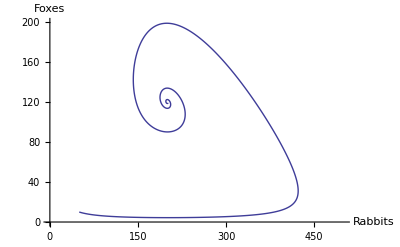

```mathematica
RabFox[{r_,f_},G_:0.02,K_:500] := {r +(G  (1 - (r/K)) r) - 0.0001 r f,f + (0.0001 r f) - (0.02 f)}
initPop = {50,10};
ListLinePlot[ NestList[RabFox,initPop,1500],PlotRange->{{0,500},{0,200}},AxesLabel->{"Rabbits","Foxes"}]
```

This shows the rabbit population doing what rabbits do for many generations as the fox population slowly increases due to the increasing food supply. An inflection point is reached, and the fox population begins to take off with a resulting collapse in the rabbit population. Eventually the system reaches equilibrium.

Discussion

The equation for rabbits assumes that rabbits follow the logistic model of exponential growth limited by the carrying capacity of the environment and then subtracts a term proportional to the number of rabbits and foxes where the constant 0.0001 reflects the efficiency of the predators. The equation for foxes assumes that the fox population is proportional to the ability to catch rabbits (same term from first equation) minus some natural death rate (here 2 percent of the population).

NestList provides a very simple solution to this model, but it is not the best choice if, due to efficiency, you want to create an interactive model using Manipulate. Luckily, Mathematica 7 has new capabilities for discrete math that provide an alternate solution path. RecurrenceTable is a new function that will generate the list of solutions of specified length given a recurrence relation.

```mathematica
DynamicModule[{pop},
Manipulate[
pop = RecurrenceTable[{
R[t+1] == R[t] + G * (1 - (R[t]/k))*R[t] - 0.0001 R[t] F[t],
F[t+1] ==F[t] + 0.0001  R[t] F[t] - 0.02F[t],
R[0] ==  P[[1]],
F[0] == P[[2]]},{R,F},{t,0,T},Method->{Compiled->False}];
ListLinePlot[pop,PlotRange->{{0,500},{0,200}},AxesLabel->{"Rabbits","Foxes"},PlotLabel:> Floor[Last[pop]]],
{{G,0.02},0.00,0.03},{{k,500},300,800},{{P,{50,10}},Locator},{{T,1000},1,5000,1},SaveDefinitions->True]]
```

This interactive model allows you to position the locator at the initial population levels for rabbits and foxes and allows you to adjust the growth rate, carrying capacity, and number of iterations. The plot title displays the end value of rabbits and foxes.

See Also

More elaborate predator-prey models can be found at the Wolfram Demonstration Project: http://bit.ly/mUVGS and http://bit.ly/21GfLm.

ChapterLabel.Heading1  Solving Basic Rigid Bodies Problems

Problem

You want to compute mass, center of mass, and moment of inertia as a prerequisite to solving dynamical problems involving rigid bodies.

Solution

The basic equation for computing the center of mass given a collection of discrete point masses is

(∑_(i=1)^n cm_i m_i)/(∑_(i=1)^n m_i)

where cm_i is the center of mass of each point and m_i is its mass. The numerator of this equation is called the first moment. Another name for the center of mass is the centroid.

```mathematica
centerMass[particles_] := Module[{totalMass, firstMoment},
{firstMoment,totalMass } = Sum[{mass@particles[[i]] centroid@particles[[i]], mass@particles[[i]]}, {i,Length[particles]}];
firstMoment/ totalMass]
```

```mathematica
mass@car = 1000.;
centroid@car = {100,100};
mass@driver = 86.;
centroid@driver = {103,101} ;
mass@fuel = 14.2;
centroid@fuel = {93,100};
centerMass[{car,driver,fuel}]
```

{100.144,100.078}

Discussion

The solution is fairly elementary from a physical point of view, but it may look a bit mysterious from a Mathematica coding point of view. The solution is coded using Mathematica’s prefix notion. Recall that f@x is prefix notation for f[x]. This notation is appealing for modeling problems because it is concise and readable (simply replace the @ with “of” as you read the code). Notice how I use the same notation with the problem objects car, driver, and fuel.

Now suppose this notation does not appeal to you; perhaps you like to model the physical objects as lists or some other notation like object[{mass,centroid}]. Does this mean you need to reimplement the centerMass function? Not at all. Simply define the function’s mass and centroid for your preferred representation, and you are all set.

```mathematica
mass[object[{m_,___}]] := m
```

```mathematica
centroid[object[{_,c_,___}]] := c
```

```mathematica
centerMass[{object[{1000,{100,100}}],object[{86,{103,101}}],object[{14.2,{93,100}}]}]
```

{100.144,100.078}

Another important property of rigid bodies is the mass moment of inertia about an axis. These values are important when solving problems involving rotation of the body. The general equation for the mass moment of inertia involves integration over infinitesimal point masses that make up the body, but in practice problems, equations for known geometries are typically used. One way to approach this in Mathematica is to use a property called shape and rely on pattern matching to select the appropriate formula. Each of these functions returns a list in the form {Ixx, Iyy, Izz}, giving the moment of inertia about the x-, y-, and z-axis, respectively.

```mathematica
massMomentOfInertia[o_] /; shape@o == "circularCylinder" := Module[{i1,i2},
i1=((mass@o  radius@o^2)/4) + ((mass@o length@o ^2)/12);
i2 = ((mass@o  radius@o^2)/2) ;
 {i1,i1,i2} ]
massMomentOfInertia[o_] /; shape@o == "circularCylindricalShell" := Module[{i1,i2},
i1=((mass@o  radius@o^2)/2) + ((mass@o length@o ^2)/12);
i2 = ((mass@o  radius@o^2)) ;
 {i1,i1,i2} ]
massMomentOfInertia[o_] /; shape@o == "rectangularCylinder" := Module[{ixx,iyy,izz},
ixx=((mass@o  (height@o +  length@o)  ^2)/12) ;
iyy = ((mass@o (width@o +  length@o)  ^2)/12) ;
izz =((mass@o (width@o +  height@o)  ^2)/12) ; 
 {ixx,iyy,izz} ]
massMomentOfInertia[o_] /; shape@o == "sphere" := Module[{i},
i=(mass@o  (2 radius@o ^2)/5) ;
 {i,i,i} ]
massMomentOfInertia[o_] /; shape@o == "sphericalShell" := Module[{i},
i=(mass@o  (2 radius@o ^2)/3) ;
 {i,i,i} ]
```

```mathematica
shape@car ="rectangularCylinder";
length@car = 4.73;
width@car = 1.83;
height@car = 1.25;
```

```mathematica
massMomentOfInertia[car]
```

{2980.03,3586.13,790.533}

```mathematica
shape@car ="circularCylindricalShell";
radius@car = 1.83;
```

```mathematica
massMomentOfInertia[car]
```

{3538.86,3538.86,3348.9}

ChapterLabel.Heading1  Solving Problems in Kinematics

Problem

You want to demonstrate standard problems in kinematics, like those you typically find in first-year physics studies.

Solution

The basic equations of kinematics are as follows.

```mathematica
acceleration1[deltaT_, v1_,v2_] := (v2 - v1) / deltaT
acceleration2[deltaT_, v1_,deltaS_] := 2(deltaS - v1 deltaT) / (deltaT^2)
acceleration3[v1_,v2_,deltaS_] := (v2^2 - v1^2)/ (2 deltaS)
distance[a_,v1_,deltaT_] := (a deltaT^2 /2) + v1 deltaT
distance1[a_,v1_,v2_] :=(v2^2 - v1^2) / (2 a)
distance2[deltaT_,v1_,v2_] := (deltaT/2)(v1 + v2)
time1[a_,v1_,v2_] := (v2 - v1)/ a
time2[a_,v1_,deltaS_] :=(Sqrt[v1^2 + 2 + 2 a deltaS] - v1) / a
time3[v1_,v2_,deltaS_] :=( 2 deltaS) / (v1 + v2)
velocity1[a_,v2_,deltaT_] := v2 - a deltaT
velocity2[a_,deltaS_,deltaT_] := (deltaS/deltaT)  -( a deltaT/2)
velocity3[a_,v2_,deltaS_] := Sqrt[v2^2 - 2 a deltaS]
```

Given these equations, you can solve a variety of problems. For example, how far will a bullet drop if shot horizontally from a rifle at a target 500 m away if the initial velocity is 800 m/s? Ignore drag, wind, and other factors.

First, compute how long the bullet remains in flight before hitting the target by taking the initial and final velocity to be the same.

```mathematica
timeTraveled = time3[800,800, 500] // N
```

0.625

Given the acceleration due to gravity is 9.8 m/s^2, compute the distance dropped by setting the initial vertical velocity component to zero.

```mathematica
distanceDropped = distance[9.8,0,timeTraveled]
```

1.91406

The bullet drops almost 2 meters.

Discussion

The solution works out a simple problem by working first in the x direction and then plugging the results into an equation in the y direction. In more complex problems, it is often necessary to use vectors to capture the velocity components in the x, y, and z directions. Consider a game or simulation involving a movable cannon and a movable target of varying size.

Imagine the cannon is fixed to the side of a fortress such that the vertical height (z direction in this example) is variable but the x and y position is fixed. The length, angle of elevation (alpha), left-right angle (gamma), and muzzle velocities are also variable. You require a function that gives the locus of points traversed by the shell given the cannon settings and the time of flight. Here we use Select to filter the points above ground level (positive in the z direction). The function returns a list of values of the form {{x1,y1,z1,t1}, ..., {xn,yn,zn,tn}}, where each entry is the position of the shell at the specified time. Chop is used only to replace numbers close to zero by zero. Note that in each dimension, the basic kinematic equations are in play, but since the inputs are in terms of angles, some basic trigonometry is needed to get the separate x, y, and z components. Velocity is constant in the x-y plane (we are still ignoring drag), and the z-axis uses the initial velocity component and the fall of the shell due to gravity.

```mathematica
displacement[origin_List,velocity_,alpha_,gamma_,tEnd_] := With[{g=9.8},
Select[If [tEnd ≤ 0,{},
Chop[Table[{
origin[[1]] + velocity *t *  Cos[alpha * Pi/2],
origin[[2]] + velocity * t  *  Cos[gamma * Pi],
origin[[3]] + velocity * t  *  Sin[alpha * Pi/2] - 0.5  g t^2,
t},
{t,0,tEnd,0.25}]]],#[[3]]≥0&]
]
```

You can also create a function that computes the instantaneous velocity components at a specified time.

```mathematica
velocity[velocity_,alpha_,gamma_,t_] :=
With[{g=9.8},
 Chop[
If[t>0,
{velocity  *  Cos[alpha * Pi/2],
velocity *  Cos[gamma * Pi],
velocity Sin[alpha * Pi/2] - g t},{0.,0.,0.}]
]
]
```

Since the plan is to create a simulation, you need a function that figures out when the shell intersects with the target. For simplicity, assume the shape of the target is a box.

```mathematica
intersect[point_List,corner1_List,corner2_List] := 
point[[1]] ≥ corner1[[1]] && point[[1]] ≤  corner2[[1]] &&
point[[2]] ≥ corner1[[2]] && point[[2]] ≤  corner2[[2]] &&
point[[3]] ≥ corner1[[3]] && point[[3]] ≤  corner2[[3]]
(*The shell hit the target if any point in the locus of points intersects. Apply Or to list of Booleans.*)
intersection[points_List,corner1_List,corner2_List] := Or @@(intersect[#,corner1,corner2]& /@ points)
```

You can set the simulation up inside of a Manipulate so that you can play around with all the variables.

```mathematica
With[{width=200,height=200,length=200,limit=10},
Manipulate[
DynamicModule[{b,Lx,Ly,Lz,cannonAlpha,cannonGamma,targetX,targetY,path,text,color,Vx,Vy,Vz},
{cannonGamma,cannonAlpha} = cannonOrient;
{targetX,targetY} = targetPos;
b =  cannonL  * Cos[(1 - cannonAlpha) * Pi/2];
Lx =  cannonL Cos[cannonAlpha * Pi/2];
Ly =length/2 + cannonL *  Cos[cannonGamma * Pi];
Lz = cannonL Sin[cannonAlpha * Pi/2];
path = displacement[{Lx,Ly,cannonZb+Lz},cannonVM,cannonAlpha,cannonGamma,time];
tLast = If[Length[path]>1,Last[path][[4]],0];
{Vx,Vy,Vz} = velocity[cannonVM,cannonAlpha,cannonGamma,tLast];
color =If[intersection[path,{targetX,targetY,targetZ},{targetX+targetL,targetY+targetW,targetZ+targetH}],Red,Green];
Column[{
Grid[{{"Vx","Vy","Vz"},{Vx,Vy,Vz}}],
Graphics3D[{{Thickness[0.02],Line[{{0,length/2,cannonZb},{Lx,Ly,Lz+cannonZb}}]},{color,Cuboid[{targetX,targetY,targetZ},{targetX+targetL,targetY+targetW,targetZ+targetH}]},Point[Most[#]]&/@ path},
PlotRange->{{0,width},{0,length},{0,height}},ImageSize->300]}]
],
{{cannonVM,50},10,100},{{cannonOrient,{0.5,0.5}},{0,0},{1,1}},{cannonL,20,length/2},{cannonZb,0,height/2}, 
{{targetPos,{100,100}},{5 * limit,0},{width-limit,length-limit}},
{targetZ,0,height-limit},{targetL,limit,length/2},{targetW,limit,width/2},{targetH,limit,height/2},
{time,0,25},
{time,0,25,ControlType->Trigger},SaveDefinitions->True]]
```

The initial output of the Manipulate is shown in Out[85] above. The path of the bullet is displayed up until the point in time specified by the time control, so the box turns red after it is hit by a shell. The instantaneous velocity of the shell is displayed for the current value of time. The Vz will be negative when the shell is falling. Figure 13-1 shows two frames from the Manipulate, at a time before impact and a time after.

See Also

David M. Bourg’s Physics for Game Developers (O’Reilly) has an example of the cannon problem where wind drag is introduced. Keep in mind that the author uses the y-axis as the vertical whereas the code in this recipe uses the z-axis.

Mathematical Methods Using Mathematica by Sadri Hassani (Springer) has solutions to similar problems using differential equations which consider drag, curvature of the earth, and nonconstant acceleration at large distances from the earth’s surface (see Chapter 6).

-Graphics-
-Graphics-

Two frames from the cannon simulation

ChapterLabel.Heading1  Computing Normal Modes for Coupled Mass Problems

Problem

You want to compute the normal modes for a system of identical masses connected by identical springs. Normal modes are natural or resonant frequencies of the entire system. The system this recipe considers consists of n>1 masses connected by n-1 springs on a frictionless surface. Figure 13-2 shows an example for n=3.

Coupled masses

Solution

Here I state, without proof (refer to “See Also” section on page 532), that these systems take the form of n simultaneous linear equations whose matrix representation is tridiagonal. That is a matrix with nonzero entries along the main diagonal and adjacent minor diagonals and zero entries in all other elements. The corner entries of the main diagonal are special since they represent masses that are free on one side and take the form k - m*ω^2, where k is the spring constant, m is the mass, and ω is the angular frequency. The off corner entries represent the masses with springs on both sides and take the form 2*k - m*ω^2. The minor diagonals are all -k. Here I solve the three mass problems, and in the discussion, I show how to create a general solver for the n mass case.

```mathematica
matrix=({{k-2ω^2, -k, 0}, {-k, 2k-2ω^2, -k}, {0, -k, k-2ω^2}})
```

{{k-2 ω^2,-k,0},{-k,2 k-2 ω^2,-k},{0,-k,k-2 ω^2}}

Nontrivial solutions to this system leave the matrix as noninvertible; hence, the determinant is zero. Use Solve to find the frequencies in terms of k.

```mathematica
sol =Solve[Det[matrix] == 0, ω]
```

{{ω→0},{ω→0},{ω→-√(3/2) √k},{ω→√(3/2) √k},{ω→-(√k)/(√2)},{ω→(√k)/(√2)}}

You don’t care about the solutions with negative or zero frequencies, so you can filter these out to obtain two physically interesting resonant frequencies.

```mathematica
sol =Cases[sol,Except[{_ -> 0} | {_ -> -_}]]
```

{{ω→√(3/2) √k},{ω→(√k)/(√2)}}

Given the frequencies, you can solve the system to get the amplitudes. The first solution gives a1 == a3 and a2 == -2a1, with the alternative of k == 0 being physically uninteresting. This solution has the outer masses moving in unison in the same direction while the inner mass compensates by moving in the opposite direction with twice the amplitude.

```mathematica
Reduce[Dot[(matrix /. sol[[1]]) ,{a1,a2,a3}]== 0,{a1,a2,a3}]
```

(a2==-2 a1&&a3==a1)||k==0

The second solution gives a2 == 0 and a3 == -a1 with the alternative of k == 0 being physically uninteresting. This is a solution with the center mass at rest and the outer masses moving toward and then away from the center.

```mathematica
Reduce[Dot[(matrix /. sol[[2]]) ,{a1,a2,a3}]== 0,{a1,a2,a3}]
```

(a2==0&&a3==-a1)||k==0

Discussion

To solve the general n-mass system, we need a way to synthesize a tridiagonal matrix of the proper form. For this, SparseArray and Band are just what the doctor ordered. When using sparse matrix, rules that come earlier override rules that come later. This works to your favor because it allows the case where n == 2 to be handled without any conditional logic stemming from the fact that there are no 2*k - m*ω^2 terms when n == 2.

```mathematica
Clear[massMatrix];
massMatrix[n_/;n>1] := SparseArray[{
{1,1} ->k-m ω^2,
{n,n}->k-m ω^2,
Band[{2,1}]->-k,
Band[{1,2}]->-k,
Band[{1,1}]->2k-m ω^2},n]
```

```mathematica
massMatrix[2] //MatrixForm
```

(k-m ω^2 | -k
-k | k-m ω^2)

```mathematica
massMatrix[5]//MatrixForm
```

(k-m ω^2 | -k | 0 | 0 | 0
-k | 2 k-m ω^2 | -k | 0 | 0
0 | -k | 2 k-m ω^2 | -k | 0
0 | 0 | -k | 2 k-m ω^2 | -k
0 | 0 | 0 | -k | k-m ω^2)

For the general solution, you want to use NSolve with specific values of m and k because roots of polynomials with degree greater than five are likely to give Solve trouble. Here I solve a 10-mass system with k == 1 and m == 1. Chop is used to remove residual imaginary values and Cases filters out zero and negative solutions because they are physically uninteresting.

```mathematica
Cases[Chop[NSolve[Det[massMatrix[10]]==0 /. {k->1,m->1},ω]],{_->a_/;a>0}]
```

{{ω→0.312869},{ω→0.618034},{ω→0.907981},{ω→1.17557},{ω→1.41421},{ω→1.61803},{ω→1.78201},{ω→1.90211},{ω→1.97538}}

See Also

You can find derivations of the systems solved in this recipe in many advanced physics and linear algebra books. In particular, Mathematical Methods Using Mathematica by Sadri Hassani provides a nice mix of practical physics and Mathematica techniques, although the most recent edition is written for versions of Mathematica prior to 6 and therefore does not always indicate the best technique to use for current versions.

ChapterLabel.Heading1  Modeling a Vibrating String

Problem

You want to model the dynamics of a vibrating string after it is released from a particular deformation.

Solution

This solution is a particular solution to the one-dimensional wave equation D[u[x,t], {x,2}] == c^2 D[u[x,t],{t,2}] where u[x,t] gives the position of the string at point x and time t. The general solution to the wave equation can be obtained using DSolve.

```mathematica
DSolve[D[u[x,t],{x,2}] == c^2 D[u[x,t],{t,2}],u[t,x],{t,x}]
```

{{u[x,t]→C[1][t-√(c^2) x]+C[2][t+√(c^2) x]}}

The general solution is not very helpful because it is specified in terms of two unknown functions, C[1] and C[2]. In theory, you could specify boundary conditions and initial conditions, but DSolve is very limited in its ability to find solutions to partial differential equations. This problem is better handled numerically with NDSolve.

First we need a specification for the shape of the string at t = 0. For simplicity, I’ll use the Sin function that will give a width of L units. Here I use Plot to show the initial defection of the string.

```mathematica
string[x_,L_]:=0.35 Sin[(π x)/L];
```

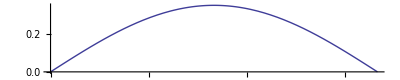

```mathematica
With[{L=5},Plot[string[ x,L],{x,0,L},AspectRatio->1/L]]
```

To use NDSolve to model the vibrating string, you must provide initial and boundary conditions. The initial condition states that u[0,x] = string[x]. In other words, at the start, the string has the position depicted previously. You must also specify the initial velocity of the string, which is the first derivative with respect to time. The obvious choice for initial velocity is zero. Using input form, this would be entered as Derivative[1, 0][u][0, x] == 0. This operator notation was explained in Recipe 11.4. The two boundary conditions specify that the ends of the string are anchored at position 0 and L, u[t, 0] == 0, and u[t, L] == 0.

```mathematica
With[{L = 5,T=10,waveEq = D[u[t, x], t, t] == D[u[t, x], x, x]}, 
sol=NDSolve[{waveEq, u[0, x] == string[x,L], Derivative[1, 0][u][0, x] == 0, 
     u[t, 0] == 0, u[t, L] == 0}, u, {t, 0, 10}, {x, 0, L}];
Animate[Plot[Evaluate[u[t,x] /. sol[[1]]],{x,0,L},AspectRatio->1/L,PlotRange->{{0,L},{-0.4,0.4}}],{t,0,T,0.5},SaveDefinitions->True]]
```

Discussion

Although DSolve can deal with some partial differential equations (PDEs), it is limited in its ability to derive specific solutions given initial and boundary conditions. Therefore, it is better to use NDSolve on PDEs, as I’ve done in the solution. However, it is not difficult to pose problems that NDSolve will have a hard time with and ultimately fail to solve. Consider trying to solve the wave equation with an initial position that contains a discontinuity.

```mathematica
string2[x_,L_] := 0.7 Abs[ x /L- Round[x/L]]
```

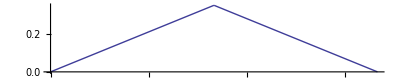

```mathematica
With[{L=5},Plot[string2[ x,L],{x,0,L},AspectRatio->1/L]]
```

If you try to use string2 in the solution shown in In[99] above, it will likely run for a very long time, consuming memory and finally failing. However, this situation is not entirely hopeless. One technique is to produce an approximation to string2 using Fourier series. Using Fourier series, I obtained the following Sin expansion, called sinString2:

```mathematica
sinString2[x_] =0.285325252629769 Sin[(Pi*x)/5]-0.033193742967516204 Sin[(3*Pi*x)/5]+0.013117204588138661 Sin[π x]-0.007723288156504195 Sin[(7*Pi*x)/5]+0.005695145921372713 Sin[(9*Pi*x)/5]-0.004945365736699312 Sin[(11*Pi*x)/5];
```

Below I plot both functions to demonstrate how closely sinString2 approximates string2 while smoothing out the discontinuity at the apex.

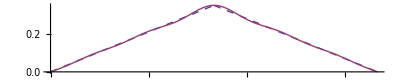

```mathematica
With[{L=5},Plot[{string2[ x,L],sinString2[x]},{x,0,L},AspectRatio->1/L,PlotStyle->{Dashed,Thin}]]
```

```mathematica
With[{L = 5, T = 10, waveEq = D[u[t, x], t, t] == D[u[t, x], x, x]}, 
 sol2 = NDSolve[{waveEq, u[0, x] == sinString2[x], Derivative[1, 0][u][0, x] == 0, 
         u[t, 0] == 0, u[t, L] == 0}, u, {t, 0, 10}, {x, 0, L}];
 Animate[Plot[Evaluate[u[t, x] /. sol2[[1]]], {x, 0, L}, AspectRatio -> 1/L, PlotRange -> {{0, L}, {-0.40, 0.40}}], {t, 0, T, 0.5},SaveDefinitions->True]]
```

There is an exact solution to the triangular wave, although it isn’t derived here (refer to the “See Also” section on page 536). It is given by this infinite sum, which Mathematica can solve using a special function LerchPhi. This solution is too complex to use in an animation, but you can use it to verify that the approximate solution is quite good.

```mathematica
triangular[t_, x_] = With[{L = 5}, FullSimplify[((0.35*8)/Pi^2)*Sum[(-1)^(i + 1)*Sin[(2*i - 1)*Pi*(x/L)]*
       (Cos[(2*i - 1)*Pi*(t/L)]/(2*i - 1)^2), {i, 1, Infinity}]]]
```

ⅇ^(-1/5 ⅈ π (5 t+x)) ((0.-0.0177312 ⅈ) ⅇ^(2/5 ⅈ π (2 t+x)) LerchPhi[-ⅇ^(-2/5 ⅈ π (t-x)),2,1/2]+(0.+0.0177312 ⅈ) ⅇ^((6 ⅈ π t)/5) LerchPhi[-ⅇ^(2/5 ⅈ π (t-x)),2,1/2]+(0.+0.0177312 ⅈ) ⅇ^((4 ⅈ π t)/5) LerchPhi[-ⅇ^(-2/5 ⅈ π (t+x)),2,1/2]-(0.+0.0177312 ⅈ) ⅇ^(2/5 ⅈ π (3 t+x)) LerchPhi[-ⅇ^(2/5 ⅈ π (t+x)),2,1/2])

Plotting a few snapshots of the exact solution over time tells us that the approximate solution is more than adequate and, in some sense, superior because it is far less computationally intense.

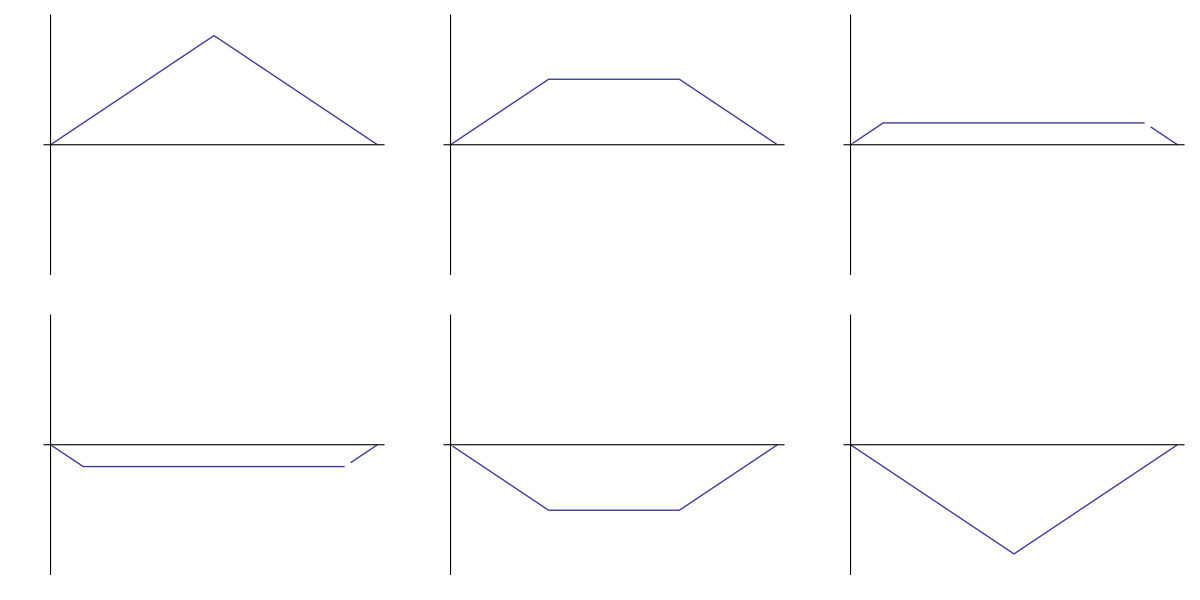

```mathematica
Grid[With[{L=5,T=5},Partition[Table[Plot[triangular[t, x] , {x, 0, L},
 AspectRatio -> 1/L,Ticks->None, PlotRange -> {{0, L}, {-0.40, 0.40}}], {t, 0, T}],3]]]
```

See Also

There are many ways to approach the solution to the wave equation. When this problem is solved by hand, separation of variables is often employed. See Advanced Engineering Mathematics by Erwin Kreyszig (John Wiley) for a step-by-step example. Warning: this book is not a Mathematica reference, but the problems are worked out in enough detail that you can easily see your way to creating your own Mathematica-based solutions.

ChapterLabel.Heading1  Modeling Electrical Circuits

Problem

You want to understand how electrical circuits consisting of resistors, capacitors, and inductors behave.

Solution

The differential equation governing an RLC circuit is L I'' + R I' + I/C = E(t), where I is current, L is inductance, R is resistance, C is capacitance, and E(t) is the electromotive force (commonly known as voltage). Modeling the system means understanding how the current varies as you drive the system with a particular timing varying voltage. Let’s consider a common sinusoidal voltage and solve the system assuming that the charge and current are zero at t=0. Setting the problem up with the context of a With allows you to solve the problem for different values of inductance, capacitance, resistance, frequency, and voltage.

```mathematica
sol =With[{L = 0.01,R = 100,C = 0.001,f=60,V = 1},DSolve[{L Iout''[t] + R Iout'[t] + 1/C Iout[t] ==V 2 Pi f Cos[2 Pi f t], Iout[0] == 0,Iout'[0]==0},Iout[t],t]]
```

{{Iout[t]→ⅇ^(-10000. t) (0.000377588 ⅇ^(10.01 t)-0.000265869 ⅇ^(9989.99 t)-(0.000111719+0. ⅈ) ⅇ^(10000. t) Cos[376.991 t]+(0.00999875+0. ⅈ) ⅇ^(10000. t) Sin[376.991 t])}}

```mathematica
fIout[t_] =Chop[FullSimplify[Iout[t] /. sol[[1]]]]
```

0.000377588 ⅇ^(-9989.99 t)-0.000265869 ⅇ^(-10.01 t)-0.000111719 Cos[376.991 t]+0.00999875 Sin[376.991 t]

By plotting the input voltage and output current, you can see they have the same basic shape and frequency except for a phase shift.

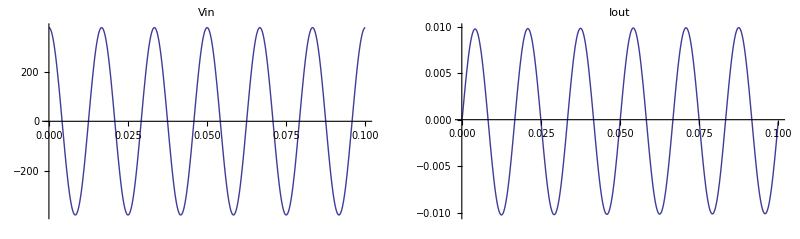

```mathematica
With[{f=60,V = 1},
GraphicsRow[{Plot[{V 2 Pi f Cos[2 Pi f t]},{t,0,0.1},PlotLabel->Vin],
Plot[{fIout[t]},{t,0,0.1},PlotLabel->Iout]}]
]
```

Discussion

A more interesting example uses a nonsinusoidal wave, such as a triangular wave. Conveniently, Mathematica 7 has a function TriangleWave[t] that suits our purpose.

```mathematica
Et[V_,t_] = V TriangleWave[t];
```

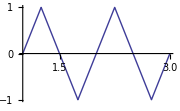

```mathematica
Plot[Et[1,t],{t,1,3},ImageSize->Small]
```

However, the discontinuities in this waveform throw DSolve for a loop. To work around this, represent the triangular wave by its Fourier series. This will give a very close approximation without the discontinuities at the extremes. This will allow you to use DSolve.

```mathematica
Et2[V_,t_] = FourierSinSeries[Et[V,t],t,10,FourierParameters->{1,2Pi}]
```

(8 V Sin[2 π t])/π^2-(8 V Sin[6 π t])/(9 π^2)+(8 V Sin[10 π t])/(25 π^2)-(8 V Sin[14 π t])/(49 π^2)+(8 V Sin[18 π t])/(81 π^2)

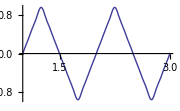

```mathematica
Plot[Et2[1,t],{t,1,3},ImageSize->Small]
```

```mathematica
sol2 = With[{L = 0.01, R = 100, C = 0.001, V = 1}, 
DSolve[{L*Derivative[2][Ii][t] + R*Derivative[1][Ii][t] + (1/C)*Ii[t] == 
       Et2[V, t], Ii[0] == 0, Derivative[1][Ii][0] == 0}, Ii[t], t]];
```

```mathematica
fIout2[t_] = Ii[t] /. sol2[[1]];
```

Notice how the RLC circuit responds to the triangular wave input by smoothing the current flow to an approximately sinusoidal form. As an exercise, you can try this same example using SquareWave, SawtoothWave, or other functions of your own design.

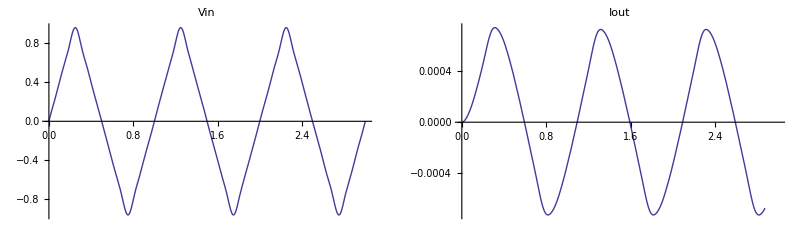

```mathematica
With[{f=60,V = 1},
GraphicsRow[{Plot[{Et2[1,t]},{t,0,3},PlotLabel->Vin],
Plot[{fIout2[t]},{t,0,3},PlotLabel->Iout]}]
]
```

ChapterLabel.Heading1  Modeling Truss Structures Using 
the Finite Element Method

Problem

You want to build a model based on the finite element method (FEM). You want to organize the model in a manner that allows you to obtain the solution as well as other intermediate results and structural diagrams.

Solution

The FEM has a wide range of engineering applications. In this recipe, I will limit the discussion to structures composed of linear elements known as trusses. See the figure shown in the “Discussion” section on page 545. Here my focus will be on the organization of the solution within Mathematica rather than on the underlying theory. Therefore, all results will be present without derivation of the underlying mathematics. Please refer to the references in the “See Also” section on page 547.

To begin, you will need a means to represent the elements. I use a structure called linearElement that specifies two endpoints called nodes ({{x1, y1}, {x2, y2}}), an area, and a measure of stiffness called Young’s Modulus (YM).

```mathematica
linearElement[{{x1,y1},{x2,y2}},area, YM]
```

In addition, you need a means for specifying the x and y components of the force at each node.

```mathematica
force[{x,y},fx,fy]
```

Furthermore, at each node there is a computed displacement in the x and y direction. The FEM literature uses the variable u for x displacements and v for y displacements Typically, each node is sequentially numbered, so you would have u1, v1, u2, v2, and so on. I will not use a sequential numbering here, because each node is uniquely identified by its coordinates, and given Mathematica’s liberal representation of variables, it is much more convenient to specify nodal displacements using coordinates.

u[x1,y1]
(*The displacement in the x direction at node {x1,y1}*)
v[x1,y1] (*The displacement in the y direction at node {x1,y1}*)

With these conventions established, I proceed by defining a series of helper functions that will be needed later. I provide a brief description of each function but, for brevity, defer more detail to the “Discussion” section on page 543.

Each element in the model is governed by a system of linear equations. The system is naturally represented by a symmetric matrix. The symmetry takes the form {{A,-A},{-A,A}} where A is a block matrix.

```mathematica
linearElementMatrix[linearElement[{{x1_,y1_},{x2_,y2_}},area_,YM_]] :=
Module[{L,BlockMatrix, LocalMatrix,A,l, m},
L = EuclideanDistance[{x1,y1},{x2,y2}];
BlockMatrix = {{A,-A},{-A,A}};
LocalMatrix =ArrayFlatten[ BlockMatrix/.{A-> {{l l,l m},{l m, m m}}}];
( LocalMatrix /.  {l -> (x2 - x1)/L , m -> (y2 -y1) /L})(( YM area)/L)
]
```

A location vector provides a means for locating the position of the local element matrices computed by linearElementMatrix within a larger global matrix that represents the system over all elements.

```mathematica
assemblyLocationVector[linearElement[{n1_,n2_},__],allnodes_]:= Flatten[Position[allnodes,#]& /@{u@@n1,v@@n1,u@@n2,v@@n2}]
```

This helper maps a node of the form {{x1,y1},{x2,y2}} to the corresponding force components {{fx1,fy1},{{fx2,fy2}}}. It does this by searching for the first match of the node within the list of forces and transforming it to the desired form.

```mathematica
getExternalForces[{forces__force},node_] := Cases[{forces},force[node,fu_,fv_]:> {fu,fv},1,1]
```

This helper extracts the unique set of nodes from the elements and places them in a canonical order, as defined by Union. This ordering is essential to the construction of a consistent system of equations. See the “Discussion” section on page 543 for details.

```mathematica
getNodes[{elements__linearElement}] := Union[{elements}/. linearElement[{n1_,n2_},__] :> Sequence[n1,n2]]
```

This helper is used to construct a replacement rule for forces.

```mathematica
makeForceRule[force[p_,fx_,fy_]] := force[p,_,_] -> force[p,fx,fy]
```

Construct a global vector of all forces using a set of nodes in canonical order.

```mathematica
getForceVector[{forces__force}, nodes_] := Flatten[getExternalForces[{forces},#]& /@ nodes]
```

Assemble the global matrix that defines the system of equations over all elements using the local matrices for individual elements and the location vectors that define the position of the local matrices with the global matrix. Note that the global matrix is obtained by summing the local matrices into the appropriate positions within the global matrix. In other words, think of each member of locationVectors as specifying a submatrix within the global matrix for which the corresponding member of localMatrices is added.

```mathematica
assembleGlobalMatrix[localMatricies_,locationVectors_,numElements_,dimension_] := 
Module[{g},
g =Table[0,{dimension},{dimension}];
Do[g[[ locationVectors[[i]],locationVectors[[i]] ]] += localMatricies[[i]],{i,1,numElements}];
g
]
```

A model consists of a collection of connected elements, the external forces applied to the structure at one or more nodes, and the boundary conditions that typically manifest as points where a node is anchored, rendered immobile in the x, y, or both directions. Here I organize a solution in the spirit of LinearModelFit covered in  Chapter 12. That is, I construct an object called a TrussModel, the function of which is to organize the underlying data and then use that object as the target for requests for certain properties relevant to the FEM. As of Mathematica 6 and particularly in Mathematica 7, this object-based methodology has emerged as a design pattern for organizing solutions that involve large quantities of data or collections of related functionality.

To proceed in this manner, you need a function for creating the TrussModel and a Format for displaying it. The Format is syntactic sugar that hides the details of the TrussModel, which could be quite large.

```mathematica
createTrussModel[{elements__linearElement},{forces___force},boundaryNodes_] := Module[{localMatrices,nodes,nodalVar,forceVec,locationVectors,degreesOfFreedom,globalMatrix,allForces,forceRules},
nodes = getNodes[{elements}];
nodalVar = Flatten[{u@@#,v@@#}&/@ nodes];
localMatrices = linearElementMatrix /@ {elements};
locationVectors = assemblyLocationVector[#,nodalVar]& /@ {elements};
globalMatrix =assembleGlobalMatrix[localMatrices,locationVectors,Length[{elements}],Length[nodalVar]];
degreesOfFreedom = Complement[Range[Length[nodalVar]],Flatten[Position[nodalVar,#]& /@ boundaryNodes]];
allForces = force[#,0,0]& /@ nodes;
forceRules = makeForceRule /@ {forces} ;
allForces = allForces /. forceRules;
forceVec = getForceVector[allForces,nodes];
TrussModel[{elements},boundaryNodes,localMatrices,globalMatrix,nodalVar,forceVec,degreesOfFreedom,forces]]

Format[TrussModel[elements_,boundaryNodes_,__]] := ToString[TrussModel[{Length[elements]},{Length[boundaryNodes]}]]
```

The goal of a FEM analysis is to determine the behavior of the structure from the behavior of the elements. For a system of trusses, solve for the displacements at the joints, the axial forces, and axial stresses. Following the proposed methodology, these will be accessed as properties of the TrussModel.

The displacements property is implemented as a functional pattern associated with the TrussModel. This notation may look somewhat unusual but is quite natural from the standpoint of Mathematica’s design. It simply states that when you see a pattern consisting of a TrussModel and a literal argument, "displacements", replace it with the results of computing the displacements using data from the TrussModel.

```mathematica
TrussModel[_,_,_,globalMatrix_,nodalVars_,forceVec_,degreesOfFreedom_,___]["displacements"] := 
Flatten[Solve[Dot[globalMatrix[[degreesOfFreedom,degreesOfFreedom]],nodalVars[[degreesOfFreedom]]]  == forceVec[[degreesOfFreedom]],nodalVars[[degreesOfFreedom]]]]
```

As a matter of convenience, you can make a property the default property of the model by associating it with the invocation of the model with no arguments. Of course, thus far I have defined only one property, displacements, but it was my intent to make this the default. In the discussion I derive other properties of this model.

```mathematica
TrussModel[model__][] := TrussModel[model]["displacements"]
```

All this tedious preparation leads us to a solution that is very easy to use. Here is the TrussModel, depicted in Out[136] on page 545. The example data is borrowed from a problem presented in Bhatti’s book (refer to the “See Also” section on page 547).

```mathematica
tm = createTrussModel[{linearElement[{{0,0},{1500,3500}},4000.,200*10^3],
linearElement[{{1500,3500},{5000,5000}},4000.,200*10^3],
linearElement[{{0,0},{0,5000}},3000.,200*10^3],
linearElement[{{0,5000},{5000,5000}},3000.,200*10^3],
linearElement[{{0,5000},{1500,3500}},2000.,70*10^3]},
{force[{1500,3500},0,-150000]},
{u[0,0],v[0,0],u[5000,5000],v[5000,5000]}]
```

TrussModel[{5}, {4}]

Now you can compute the nodal displacements at the nodes that are unsupported.

```mathematica
tm["displacements"]
```

{u[0,5000]→0.264704,v[0,5000]→-0.264704,u[1500,3500]→0.538954,v[1500,3500]→-0.953061}

Discussion

To complete the TrussModel, we need to define more properties. It is nice to have a visual aid to help diagnose problems in the setup of the model. A "diagram" property generates graphics. As before, I need to develop some helper functions to take care of certain tails. Each helper function has a placeholder for options (opts___), but to keep the implementation from getting any more complicated, I do not implement any options. You could add options to control the level of detail, for example, to include or suppress displacement arrows and labels. Other options might be pass-through options to Graphics.

The diagram uses a convention where supported nodes are filled-in points, whereas unsupported nodes are hollow circles with associated displacement arrows. It is possible that a node can be stationary in one direction but not the other. For example, a roller would be free to move in the x direction but not the y. Professional FEM software handles a much wider variety of boundary conditions, and standard icons are used in the industry to depict these. The goal here is simplicity over sophistication.

The function trussGraphicsNodes does most of the work of mapping the various types of nodes onto the specific graphics element. The complexity of the code is managed by judicious use of patterns and replacement rules. Some of the scaling and text placement was largely determined by trial and error, so you may need to tweak these settings for your own application or add additional code to help generalize the solution.

```mathematica
trussGraphicsElement[linearElement[{{x1_,y1_},{x2_,y2_}},___],opts___] := 
{Opacity[0.6],Line[{{x1,y1},{x2,y2}}]}

trussGraphicsNodes[nodalVars_, boundaryNodes_,arrowLen_,opts___] := Module[{freeNodes,arrows,circles,disks},
freeNodes = Complement[nodalVars,boundaryNodes] ;
arrows ={ Arrowheads[.02],
freeNodes /. {u[x_,y_] :> {Arrow[{{x,y},{x+arrowLen,y}}],Text[u[x,y],Offset[{12,12},{x+arrowLen,y}]]},
v[x_,y_] :> {Arrow[{{x,y},{x,y+arrowLen}}],Text[v[x,y],Offset[{12,12},{x,y+arrowLen}]]}}
};
circles = Union[freeNodes /. (u|v)[x_,y_] :>  Circle[{x,y},arrowLen/6]];
disks = Union[boundaryNodes /. (u|v)[x_,y_] :>  Disk[{x,y},arrowLen/6]];
Flatten[{circles,disks,arrows}]
]

trussForceGraphics[force[{x_,y_},fx_,fy_],scale_,opts___] := Module[{a1,a2},
a1={Arrow[{{x,y},{x+fx*scale,y}}],Text[fx,Offset[{Sign[fx]12,0},{x+fx*scale,y}]]};
a2 ={Arrow[{{x,y},{x,y+fy*scale}}],Text[fy,Offset[{0,Sign[fy]12},{x,y+fy*scale}]]};
{a1,a2}
]

trussBoundary[force[{x_,y_},fx_,fy_],scale_,opts___] := Module[{a1,a2},
a1=Arrow[{{x,y},{x+fx*scale,y}}];
a2 =Arrow[{{x,y},{x,y+fy*scale}}];
{a1,a2}
]

TrussModel[{elements__linearElement},boundaryNodes_,_,_,nodalVars_,forceVec_,degreesOfFreedom_,forces_]["diagram",opts___] := 
Module[{dispLen,forceScale,min,max},
{max,min} = {Max[##],Min[##]}& @@ Flatten[List @@@ nodalVars];
dispLen = (max - min) /15;
forceScale = (max - min)/(3 Max[Abs[forceVec]]);
Graphics[{
trussGraphicsElement[#,opts]& /@ {elements} ,
trussGraphicsNodes[nodalVars, boundaryNodes,dispLen,opts],
Flatten[trussForceGraphics[#,forceScale,opts]& /@ {forces}]
},Axes->True,ImagePadding->All,AxesOrigin->{-max/10,-max/10}]]
```

As before, once the infrastructure is in place, the diagram is easy to create by simply asking the model for the "diagram" property.

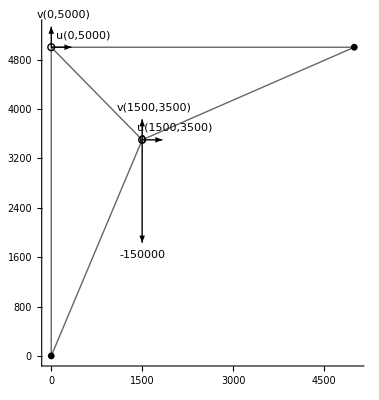

```mathematica
tm["diagram"]
```

Other important properties are axialStrain, axialStress, and axialForce. These will be implemented to return all or specific values for a specified element.

```mathematica
Clear[axialStrain]
axialStrain[linearElement[{{x1_,y1_},{x2_,y2_}},__], displacements_] :=
 Module[{l, m, L,dv},
dv ={u[x1,y1],v[x1,y1],u[x2,y2],v[x2,y2]} /. displacements /. (u|v)[__]->0;
 L = EuclideanDistance[{x1,y1},{x2,y2}];
 l = (x2 - x1)/L;
 m = (y2 - y1)/L;
Plus[-#1,#2]& @@ Dot[{{l, m, 0, 0}, {0, 0, l, m}},dv]/L]

axialStress[linearElement[_,_,YM_], strain_] := strain * YM;

axialForce[linearElement[_,A_,_], stress_] := stress * A ;
```

```mathematica
TrussModel[{elements__linearElement},__]["elements"] := {elements}
```

```mathematica
TrussModel[model__]["axial strain",element_ : All] := Module[{thisModel,disp,elements},
thisModel = TrussModel[model];
disp = thisModel["displacements"];
elements =  Cases[thisModel["elements"],element /. {All-> _}];
axialStrain[#,disp]& /@ elements]

TrussModel[model__]["axial stress",element_ : All] := Module[{thisModel,strain,elements},
thisModel = TrussModel[model];
elements =  Cases[thisModel["elements"],element /. {All-> _}];
strain = thisModel["axial strain",element];
MapThread[axialStress , {elements,strain}]]
```

```mathematica
TrussModel[model__]["axial force",element_ : All] := Module[{thisModel,stress,elements},
thisModel = TrussModel[model];
elements =  Cases[thisModel["elements"],element /. {All-> _}];
stress = thisModel["axial stress",element];
MapThread[axialForce , {elements,stress}]]
```

```mathematica
tm["axial strain"]
```

{-0.000174295,-0.0000314997,-0.0000529407,-0.0000529407,0.000320869}

```mathematica
tm["axial strain",linearElement[{{0,0},{1500,3500}},__]]
```

{-0.000174295}

```mathematica
tm["axial stress"]
```

{-34.8591,-6.29994,-10.5881,-10.5881,22.4608}

```mathematica
tm["axial force"]
```

{-139436.,-25199.8,-31764.4,-31764.4,44921.7}

See Also

There are many books and online resources that cover FEM. For example, the theory relevant to truss structures can be found at Jason Midkiff’s Virginia Tech science and engineering website: http://bit.ly/32BUq1.

If you are looking for books with a Mathematica focus, look no further than Fundamental Finite Element Analysis and Applications: With Mathematica and Matlab Computations (John Wiley) and—if you are really into FEM—Advanced Topics in Finite Element Analysis of Structures: With Mathematica and MATLAB Computations (John Wiley), both by M. Asghar Bhatti. The code in these books is pre–version 6, but I found few incompatibilities.